### Mathematica Cheat Sheet

### Generelle Funktionen

```mathematica
(*Ein Pfad hinzufügen, unter dem nach Dateien gesucht werden*)
AppendTo[$Path, ToFileName[{$HomeDirectory,"MyPackages"}]];
```

```mathematica
(*Anfang jedes Notebooks*)
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Dateien exportieren und importieren*)
Export["filename.wdx",variable,"WDX"];
variable=Import["filename.wdx"];
```

```mathematica
data=DeleteDuplicates[Cases[Import[ToFileName[NotebookDirectory[],"tabelle.data"],"Table"],{_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ}]];
```

```mathematica
(*Dynamische Variable und Ladebalken*)
i=0;maxn=450;
NIntegrate[Sin[x]x^2 Exp[-x^3],{x,-10,10},MaxPoints->maxn,PrecisionGoal->10,WorkingPrecision->6,EvaluationMonitor:>(i++;)]
Row[{ProgressIndicator[N[Dynamic[i/maxn]],{0,1}],Dynamic[N[i/maxn 100]] ,"%"}," "]
```

3.55412×10^433

%

```mathematica
(*Ladebalken für eine Tabelle*)
ProgressBar[dynvar_,varp_,varm_]:=Row[{ProgressIndicator[N[Dynamic[(dynvar-varm)/(varp-varm)]],{0,1}],Dynamic[N[(dynvar-varm)/(varp-varm) 100]] ,"%"}," "]
```

```mathematica
step=20;
ProgressBar[x,10,1]
Table[Pause[1];x,{x,1,10,(10-1)/step}]
```

%

{1,29/20,19/10,47/20,14/5,13/4,37/10,83/20,23/5,101/20,11/2,119/20,32/5,137/20,73/10,31/4,41/5,173/20,91/10,191/20,10}

```mathematica
(*Baryon number Susceptibility near the CEP for eps=h0 and T=Subscript[T, CEP]*)
step=5;
ProgressBar[mu,mup,mum]
chiBlisth0TCEP=Table[{(mu-muCEP)/muCEP,chiB[eps0,TCEP,mu]},{mu,mum,mup,(mup-mum)/step}]//Quiet;
Export["chiBlisth0_TCEP_esb.wdx",chiBlisth0TCEP,"WDX"];
```

```mathematica
(*Ab einer bestimmten Stelle die numerische Zahl abschneiden*)
Chop[]
```

```mathematica
(*Funktionen aus mehreren Ausdrücken*)
f[x_,y_]:=Block[{a,b},
Print["x="<>ToString[x]];
Print["y="<>ToString[y]];
a=x-y;
b=x*y;
a+b]
f[1,2]
```

x=1

y=2

1

```mathematica
(*Compiled Function (schneller Ausführung)*)
cf = Compile[{{x, _Real}}, Sin[x] + x^2 - 1/(1+x)];
cf[Pi]
```

9.62815

### Integrale

```mathematica
(*Numerisches Linienintegral in der komplexen Ebene*)
NIntegrate[1/x,{x,1,I,-1,-I,1}]//Chop
```

0.+6.28319 ⅈ

### Optionen und Funktionen für Plot

```mathematica
(*Logarithmischer DensityPlot*)
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
plotter[min_,max_]:=ListDensityPlot[liste,PlotRange->Full,ColorFunctionScaling->False,ColorFunction->(ColorData["DeepSeaColors"][LogarithmicScaling[#,min,max]]&)]
plotter[0.01,1000]
```

```mathematica
(*Logarithmischer DensityPlot mit Scale und Beschriftung*)
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
plotter[min_,max_,NumberOfTicks_]:=DensityPlot[f[x,y],{x,xm,xp},{y,ym,yp},PlotPoints->100,PlotRange->Full,FrameLabel->{"Label x","Label y"},PlotLabel->"Plotlabel",ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][LogarithmicScaling[#,min,max]]&),PlotLegends->BarLegend[{ColorData["LightTemperatureMap"],{0,1}},LegendMarkerSize->370,Ticks->({LogarithmicScaling[#,min,max],ScientificForm[#,2]}&/@(min (max/min)^Range[0,1,1/NumberOfTicks])),LabelStyle->{FontSize->18}]]
plotter[0.01,1000,4]
```

```mathematica
(*Plot mit Legende. Optionen für Placed: {Left, Center, Right},{Bottom, Center,Top}*)
LogPlot[{f1[x],f2[x],f3[x]},{x,xm,xp},FrameLabel->{"Label x","Label y"},Frame->True,LabelStyle->{FontSize->11},ImageSize->{600,400},PlotLegends->Placed[
LineLegend[
{Text[Style["f1",FontSize->13]],
Text[Style["f2",FontSize->13]],
Text[Style["f3",FontSize->13]]},
LegendLayout->{"Column/Row",1}],{Right,Center}]]
```

```mathematica
(*Rasterize benutzen um die Plotlegende mit dem Plot zu verbinden (besser für den Export)*)
Rasterize[Plot[],RasterSize->100]
```

```mathematica
(*Option von Plot für dickere Linien und Farbe*)
PlotStyle->{Directive[Red,AbsoluteThickness[2]]}
PlotStyle->{Dashed}
```

```mathematica
(*Text/Beschriftungen im Plot (einbinden mit Show[])*)
Graphics[{Yellow,FontSize->18,Text["text",{xCoord,yCoord}]}]
```

```mathematica
(*Plot exportieren*)
plot=Plot[x^2,{x,0,1}];
Export["Plot.pdf",plot,"PDF"]
Export["Plot.eps",plot,"EPS"]
```

Plot.pdf

Plot.eps

### Operationen auf Listen

```mathematica
(*Minialer oder Maximaler Wert einer Liste*)
Min[list]
Max[list]
```

```mathematica
(*Position eines bestimmten Wertes in einer Liste*)
Position[{a,b,c,d}, c]
```

```mathematica
(*Einen bestimmten Wert aus einer Liste löschen*)
Delete[{a,b,c,d},3]
```

```mathematica
(*Eine Funktion auf den ersten Wert einer mehrdimensionalen Liste anwenden*)
list={{a,b},{c,d}};
XLogList[alist_]:=Map[{Sign[#[[1]]]Log[Abs[#[[1]]]],#[[2]]}&,alist]
XLogList[list]
```

{{Log[Abs[a]] Sign[a],b},{Log[Abs[c]] Sign[c],d}}

```mathematica
(*Zwei Listen zusammenfügen, so dass die x-Werte unverändert bleiben, die y-Werte allerdings addiert werden*)
list1={{1,2},{3,4},{5,6}};
list2={{1,3},{3,7},{5,9}};
AddLists[alist_,blist_]:=Table[{alist[[i,1]],alist[[i,2]]+blist[[i,2]]},{i,1,Length[alist]}]
AddLists[list1,list2]
```

{{1,5},{3,11},{5,15}}

### Assumptions, Annahmen zur Verinfachung von Ausdrücken

```mathematica
(*Assumptions lässt Ausdrücke vereinfachen*)
$Assumptions=x>0&&y<0
Sqrt[1/x]-1/Sqrt[x]+Sqrt[1/y]-1/Sqrt[y]//FullSimplify
```

-2/(√y)

```mathematica
(*Assumptions wieder löschen*)
$Assumptions=True
Sqrt[1/x]-1/Sqrt[x]//FullSimplify
```

True

√(1/x)-1/(√x)

```mathematica
(*stärker nachhelfen, falls das nicht funktionieren sollte*)
expr=Sqrt[1/x]-1/Sqrt[x]+Sqrt[1/y]-1/Sqrt[y];
Map[Expand,expr,4]//Simplify[#,{x>0,y<0}]&//FullSimplify
```

-2/(√y)

```mathematica
1/(a+ⅈ b)*Conjugate[1/(a+ⅈ b)]//FullSimplify
ComplexExpand[1/(a+ⅈ b)*Conjugate[1/(a+ⅈ b)]]//FullSimplify
```

1/((a+ⅈ b) (Conjugate[a]-ⅈ Conjugate[b]))

1/(a^2+b^2)

```mathematica
(*weitere Annahmen*)
$Assumptions=_Symbol∈Reals
(*alle Variablen werden als reelle Zahlen behandelt:*)
$Assumptions=_∈Reals
```

```mathematica
(*Weitere Möglichkeite reelle Variablen zu definieren*)
Scan[ (RealQ[#] = True)&,{x,y} ]
Re[x+y]
```

x+y

### Nützliches

```mathematica
(*Reap und Sow um Einblick in eine Rechnung zu erhalten*)
Clear[list]
list={{a,b,c},{d,e,f}};
reap=Reap[Select[list,MemberQ[Sow[#],a]&]];
(*Diese Werte durchläuft #*)
reap[[2]]
(*Ergebnis des Ausdrucks*)
reap[[1]]
```

{{{a,b,c},{d,e,f}}}

{{a,b,c}}

```mathematica
(*Function to get the coefficient of an factorial expression*)
Clear[Helper1,Helper2,DenCoefficient]
Helper1[expr_,denom_]:=
Module[{f},f/;
NumericQ[Denominator[f=Simplify[expr*denom]]]
&&Not[NumericQ[Denominator[expr]]]
&&NumericQ[Simplify[Denominator[Simplify[f/denom]]/denom]]]
Helper1[expr_,denom_]:=
Module[{f},0/;
Not[NumericQ[Denominator[Simplify[f=expr*denom]]]]
||NumericQ[Denominator[expr]]
||Not[NumericQ[Simplify[Denominator[Simplify[f/denom]]/denom]]]]
Helper2[expr_,denom_]:=
Module[{hold},FullSimplify[Plus@@(Helper1[#,denom]&/@(List@@(Expand[expr]+hold)))]/.hold->0]
DenCoefficient[expr_,denom_]:=Helper2[FullSimplify[Helper2[expr,denom]/denom],denom]

DenCoefficient[a/(2(a+b^2)),(a+b^2)]
DenCoefficient[a/(2(a+b^2)),(a+b)]
DenCoefficient[a,(a+b)]
DenCoefficient[a/(a+b),(a+b)^2]
DenCoefficient[a/(a+b)^2,(a+b)^2]
DenCoefficient[a/(a+b)^2+a/(a+b)+(a+b)^2/2+b^2/(a^2+2a b+b^2),(a+b)^2]
(*should give 0:*)
DenCoefficient[a^2/(a+b)^4+2a b/(a+b)^4+b^2/(a+b)^4,(a+b)^4]
DenCoefficient[a^2/(a+b)^4+2a b/(a+b)^4+b^2/(a+b)^4,(a+b)^4]
DenCoefficient[a^4/(a+b)^4+(4*a^3*b)/(a+b)^4+(6*a^2*b^2)/(a+b)^4+(4*a*b^3)/(a+b)^4+b^4/(a+b)^4,(a+b)^4]
```

a/2

0

0

0

a

a+b^2

0

0

0

```mathematica
(*count the arguments of a function*)
ClearAll[countArgs];
SetAttributes[countArgs,{(*HoldAll,*)Listable}];
countArgs[f_Symbol]:=With[{dv=DownValues[f]},countArgs[dv]];
countArgs[Verbatim[HoldPattern][HoldPattern[f_Symbol[args___]]]:>_]:=countArgs[f[args]];
countArgs[f_[Except[_Optional|_OptionsPattern|Verbatim[Pattern][_,_OptionsPattern]],rest___]]:={1,0,0}+countArgs[f[rest]];
countArgs[f_[o__Optional,rest___]]:={0,Length[HoldComplete[o]],0}+countArgs[f[rest]];
countArgs[f_[_OptionsPattern|Verbatim[Pattern][_,_OptionsPattern]]]:={0,0,1};
countArgs[f_[]]:={0,0,0};

countArgs[f[x,1]]
countArgs[f[1,2,3]]
```

{2,0,0}

{3,0,0}

```mathematica
(*helpful function to extract parts of a function*)
Component[Amp_,n_]:=Replace[Amp,Amp[_][x__]:>{x}][[n]]
(*Get the object that gets replaced in a replacement list {a->4} => a*)
getReplacementHead[f_->_]:=f
getReplacementHead[list_]:=getReplacementHead[#]&/@list

Component[Amp[1][(a+b)^2],1]
getReplacementHead[a->4]
getReplacementHead[{a->4,b->1,c->ab}]
```

(a+b)^2

a

{a,b,c}

### FormCalc und FeynArts

```mathematica
(*Kopf*)
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
<< FeynArts`
<< FeynArtsAdd`
<< FormCalc`
<< FormCalcAdd`
ClearProcess[]
<<"!rm *.frm"
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FeynArtsAdd 1.0 (16 Dec 2016)

by Matthias Kesenheimer, with thanks to Thomas Hahn

FormCalc 9.4 (7 Jun 2016)

by Thomas Hahn

FormCalcAdd 1.2.3 (23 Jan 2016)

by Matthias Kesenheimer, with thanks to Thomas Hahn

```mathematica
SetOptions[InsertFields, Model -> "MSSMCT",Restrictions -> {NoLightFHCoupling},ExcludeParticles -> {S[1|2|3|4|5|6|11|12], F[1|2]}];
process = {F[4], -F[3]} -> {F[11], F[12]};
top = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins = InsertFields[top, process];

(*Benutzung von Diagram Select*)
(*Mit Reap und Sow kann auf lokale Variablen zugegriffen werden, hier: welche Werte durchläuft "FieldPoints"?*)
ins1 = Reap[DiagramSelect[ins,(MemberQ[Sow[FieldPoints[##]],FieldPoint[_][_,_,V[5,{_}]]]) &]]
ins1[[2]]
ins2 = Reap[ DiagramSelect[ins,(FreeQ[Sow[LoopFields[##]], V[2]] && FreeQ[Sow[LoopFields[##]], V[1]]) &]];
ins2[[2]]
ins3 = Reap[DiagramSelect[ins,(FieldMemberQ[Sow[LoopFields[##]],S[14,{_,_,_}]]) &]];
ins3[[2]]
```

```mathematica
Paint[ins1[[1]], PaintLevel -> {Classes}];
Paint[ins2[[1]], PaintLevel -> {Classes}];
Paint[ins3[[1]], PaintLevel -> {Classes}];
```

```mathematica
CreateFeynAmp[ins1[[1]]]
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

> Top. 1: 1 diagram

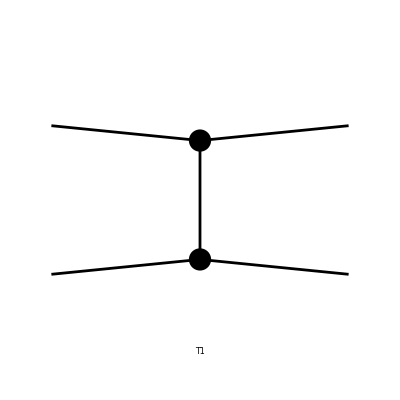

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
(*Extract Topologies*)
top = CreateTopologies[0,2->2]
top1 = Level[top,1][[3]]
top = TopologyList[top1]
Paint[top]
```